## ^183Au Fitting the negative parity bands

```mathematica
ClearAll["Global*`"]
```

### Analytical formulae

```mathematica
I0=4.5;
j=4.5;
IF[MOI_]:=1/(2*MOI);
RAD[angle_]:=angle*π/180;
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)(I+j)/2+A1*(I-j)^2-V*(2j-1)/(j+1)*Sin[γ+π/6];
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-1*(((2I-1)*(A3-A1)+2j*A1)*((2I-1)*(A2-A1)+2j*A1)+8*A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=((((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))-4I*j*A3^2)*(((2I-1)*(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ])-4I*j*A2^2));
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]-Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]+Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Energy[nw1_,nw2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](nw1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](nw2+1/2);
ExcEn[nw1_,nw2_,I_,A1_,A2_,A3_,V_,γ_]:=Energy[nw1,nw2,I,j,A1,A2,A3,V,γ]-Energy[0,0,I0,j,A1,A2,A3,V,γ];
band1Negative[I_,I1_,I2_,I3_,V_,γ_]:=SetPrecision[ExcEn[0,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]],4];
band2Negative[I_,I1_,I2_,I3_,V_,γ_]:=SetPrecision[ExcEn[1,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]],4];
```

### Experimental data

```mathematica
s1Negative=Table[N[i],{i,9/2,53/2,2}];
s2Negative=Table[N[i],{i,19/2,51/2,2}];
yrastNegative=N[{12.78,232,566,990,1492,2063,2690,3358,4050,4760,5497,6242}/1000];
tw1Negative=N[{1056,1488,1987,2540,3148,3796,4457,5133,5912}/1000];
e0Negative=yrastNegative[[1]];
yrastNegative=Table[SetPrecision[(yrastNegative[[i]]-e0Negative),4],{i,1,Length[yrastNegative]}];
tw1Negative=Table[SetPrecision[(tw1Negative[[i]]-e0Negative),4],{i,1,Length[tw1Negative]}];
```

### Fitting procedure

#### Bounds

```mathematica
i1bounds={65,85};
i2bounds={10,40};
i3bounds={1,25};
vbounds={0.01,5.0};
gmbounds={19.5,25};
(*Parameter set from mathematica*)
(*paramSetNegative={73.209,19.805,3.752,0.243,20.013};*)
```

#### Minimization function

```mathematica
chi2FuncNegative[I1_,I2_,I3_,V_,γ_]:=If[Im[Sqrt[1/(Length[s1Negative]+Length[s2Negative]+1)(Sum[(yrastNegative[[i]]-band1Negative[s1Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Negative]}]+Sum[(tw1Negative[[i]]-band2Negative[s2Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Negative]}])]]==0,Sqrt[1/(Length[s1Negative]+Length[s2Negative]+1)(Sum[(yrastNegative[[i]]-band1Negative[s1Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Negative]}]+Sum[(tw1Negative[[i]]-band2Negative[s2Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Negative]}])],10^9];
(*Parameter set for the negative bands from Python*)
(*paramSetNegative={73.209,19.805,3.752,0.243,20.013};*)
minChi2Negative=NMinimize[{chi2FuncNegative[I1,I2,I3,V,γ],i1bounds[[1]]≤I1≤i1bounds[[2]]&&i2bounds[[1]]≤I2≤i2bounds[[2]]&&i3bounds[[1]]≤I3≤i3bounds[[2]]&&vbounds[[1]]≤V≤vbounds[[2]]&&gmbounds[[1]]≤γ≤gmbounds[[2]]},{I1,I2,I3,V,γ}];
paramSetNegative=Values@minChi2Negative[[2]];
rmsValueNegative=minChi2Negative[[1]];
Print["RMS-> ",rmsValueNegative,"\nP -> ",paramSetNegative]
```

RMS-> 0.0792526
P -> {83.8748,10.0003,4.59656,0.171758,22.2022}

```mathematica
(*ListPlot[{Table[{s1Negative[[i]],yrastNegative[[i]]},{i,1,Length[s1Negative]}],Table[{s1Negative[[i]],band1Negative[s1Negative[[i]],paramSetNegative[[1]],paramSetNegative[[2]],paramSetNegative[[3]],paramSetNegative[[4]],paramSetNegative[[5]]]},{i,1,Length[s1Negative]}]},Joined->{False, True}]
ListPlot[{Table[{s2Negative[[i]],tw1Negative[[i]]},{i,1,Length[s2Negative]}],Table[{s2Negative[[i]],band2Negative[s2Negative[[i]],paramSetNegative[[1]],paramSetNegative[[2]],paramSetNegative[[3]],paramSetNegative[[4]],paramSetNegative[[5]]]},{i,1,Length[s2Negative]}]},Joined->{False, True}]*)
```

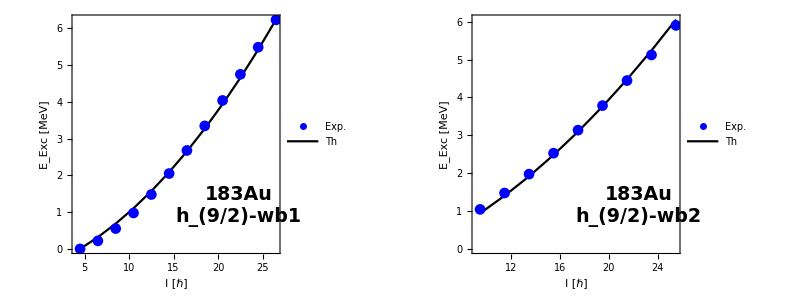

```mathematica
plotFunction[band_,params_,spins_,expData_,label_]:=ListPlot[{Table[{spins[[i]],expData[[i]]},{i,1,Length[spins]}],Table[{spins[[i]],band[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}]},Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"I [ℏ]","E_Exc [MeV]"},PlotLegends->Placed[{"Exp.","Th"},{0.25,0.75}],FrameStyle->Directive[Thick,Black],LabelStyle->{19,Black,Bold,FontFamily->"Times"},Joined->{False, True},PlotStyle->{Blue,Black},PlotMarkers->{{Automatic,11},None},Epilog->Inset[Style[label,19,Black,Bold,FontFamily->"Times"],Scaled[{0.8,0.2}]],PlotRange->Full];
pNegative1=plotFunction[band1Negative,paramSetNegative,s1Negative,yrastNegative,"183Au\nh_(9/2)-wb1"];
pNegative2=plotFunction[band2Negative,paramSetNegative,s2Negative,tw1Negative,"183Au\nh_(9/2)-wb2"];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/183-187Au_Wobbling-Bands/src/python/app/assets/plots/Au_183_plot1Negative.pdf",Show[pNegative1],ImageResolution->1200];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/183-187Au_Wobbling-Bands/src/python/app/assets/plots/Au_183_plot2Negative.pdf",Show[pNegative2],ImageResolution->1200];
Grid[{{Show[pNegative1,ImageSize->Medium],Show[pNegative2,ImageSize->Medium]}},Frame->All]
```

## Printer function

```mathematica
printer[params_]:=Do[Print[s1Negative[[i]]," ",yrastNegative[[i]]," ",band1Negative[s1Negative[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]],{i,1,Length[s1Negative]}];
```

```mathematica
pp={50,20,4,0.4,20};
chi2FuncNegative[pp[[1]],pp[[2]],pp[[3]],pp[[4]],pp[[5]]]
printer[pp]
```

0.69

4.5 0 0

6.5 0.2192 0.3003

8.5 0.5532 0.6785

10.5 0.9772 1.136

12.5 1.479 1.672

14.5 2.05 2.288

16.5 2.677 2.983

18.5 3.345 3.758

20.5 4.037 4.613

22.5 4.747 5.547

24.5 5.484 6.562

26.5 6.229 7.656